# Crypto-currencies data acquisition with visualization

## Introduction

In this notebook we show how to obtain crypto-currencies data from several data sources and make some basic time series visualizations. We assume the described data acquisition workflow is useful for doing more detailed (exploratory) analysis.

There are multiple crypto-currencies data sources, but a small proportion of them give a convenient way of extracting crypto-currencies data automatically. I found the easiest to work with to be https://finance.yahoo.com/cryptocurrencies, [YF1]. Another easy to work with Bitcoin-only data source is  https://data.bitcoinity.org , [DBO1].

(I also looked into using https://www.coindesk.com/coindesk20. )

Remark: The code below is made with certain ad-hoc inductive reasoning that brought meaningful results. This means the code has to be changed if the underlying data organization in [YF1, DBO1] is changed.

Load the paclet (not used below)

```mathematica
Needs["AntonAntonov`CryptocurrencyData`"]
```

## Yahoo! Finance

### Getting cryptocurrencies symbols and summaries

In this section we get all crypto-currencies symbols and related metadata.

Get the data of all crypto-currencies in [YF1]:

```mathematica
AbsoluteTiming[
lsData=Import["https://finance.yahoo.com/cryptocurrencies","Data"];
]
```

{7.94988,Null}

Locate the data:

```mathematica
pos=First@Position[lsData,{"Symbol","Name","Price (Intraday)","Change","% Change",___}];
dsCryptoCurrenciesColumnNames=lsData⟦Sequence@@pos⟧
Length[dsCryptoCurrenciesColumnNames]
```

{Symbol,Name,Price (Intraday),Change,% Change,Market Cap,Volume in Currency (Since 0:00 UTC),Volume in Currency (24Hr),Total Volume All Currencies (24Hr),Circulating Supply,52 Week Range,Day Chart}

12

Get the data:

```mathematica
dsCryptoCurrencies=lsData⟦Sequence@@Append[Most[pos],2]⟧;
Dimensions[dsCryptoCurrencies]
```

{25,10}

Make a dataset:

```mathematica
dsCryptoCurrencies=Dataset[dsCryptoCurrencies][All,AssociationThread[dsCryptoCurrenciesColumnNames⟦1;;-3⟧,#]&]
```

Here are the (generic) crypto-currency symbols:

```mathematica
lsCryptoCurrencySymbols=StringSplit[Normal@dsCryptoCurrencies[All,"Symbol"],"-"]⟦All,1⟧
```

{BTC,ETH,USDT,BNB,USDC,XRP,ADA,DOGE,STETH,HEX,MATIC,SOL,DOT,LTC,AVAX,SHIB,WTRX,BUSD,TRX,DAI,WBTC,LINK,UNI7083,ATOM,OKB}

### Get all time series

In this section we get all the crypto-currencies time series from [YF1].

```mathematica
AbsoluteTiming[
ccNow=Round@AbsoluteTime[Date[]]-AbsoluteTime[{1970,1,1,0,0,0}];
currencySymbol="USD";
stYFURL=StringTemplate["https://query1.finance.yahoo.com/v7/finance/download/`cryptoCurrencySymbol`-`currencySymbol`?period1=1410825600&period2="<>ToString[ccNow]<>"&interval=1d&events=history&includeAdjustedClose=true"];
aCryptoCurrenciesDataRaw=
Association@
Map[
(#<>"-"<>currencySymbol)->ResourceFunction["ImportCSVToDataset"][stYFURL[<|"cryptoCurrencySymbol"->#,"currencySymbol"->currencySymbol|>]]&,lsCryptoCurrencySymbols
];
]
```

{7.36703,Null}

Remark: Note that in the code above we specified the upper limit of the time span to be the current date. (And shifted it with respect to the epoch start 1970-01-01 used by [YF1].)

Check we good the data with dimensions retrieval:

```mathematica
Dimensions/@aCryptoCurrenciesDataRaw
```

<|BTC-USD→{3136,7},ETH-USD→{1987,7},USDT-USD→{1987,7},BNB-USD→{1987,7},USDC-USD→{1654,7},XRP-USD→{1987,7},ADA-USD→{1987,7},DOGE-USD→{1987,7},STETH-USD→{847,7},HEX-USD→{1219,7},MATIC-USD→{1452,7},SOL-USD→{1104,7},DOT-USD→{972,7},LTC-USD→{3136,7},AVAX-USD→{1010,7},SHIB-USD→{991,7},WTRX-USD→{410,7},BUSD-USD→{1307,7},TRX-USD→{1987,7},DAI-USD→{1244,7},WBTC-USD→{1540,7},LINK-USD→{1987,7},UNI7083-USD→{943,7},ATOM-USD→{1497,7},OKB-USD→{1450,7}|>

Check we good the data with random sample:

```mathematica
RandomSample[#,6]&/@KeyTake[aCryptoCurrenciesDataRaw,RandomChoice[Keys@aCryptoCurrenciesDataRaw]]
```

<|DOGE-USD→|>

Here we add the crypto-currencies symbols and convert date strings into date objects.

```mathematica
AbsoluteTiming[
aCryptoCurrenciesData=Association@KeyValueMap[Function[{k,v},k->v[All,Join[<|"Symbol"->k,"DateObject"->DateObject[#Date]|>,#]&]],aCryptoCurrenciesDataRaw];
]
```

{3.78473,Null}

### Summary

In this section we compute the summary over all datasets:

```mathematica
ResourceFunction["RecordsSummary"][Join@@Values[aCryptoCurrenciesData],"MaxTallies"->30]
```

{1 Symbol
BTC-USD | 3136
LTC-USD | 3136
ADA-USD | 1987
BNB-USD | 1987
DOGE-USD | 1987
ETH-USD | 1987
LINK-USD | 1987
TRX-USD | 1987
USDT-USD | 1987
XRP-USD | 1987
USDC-USD | 1654
WBTC-USD | 1540
ATOM-USD | 1497
MATIC-USD | 1452
OKB-USD | 1450
BUSD-USD | 1307
DAI-USD | 1244
HEX-USD | 1219
SOL-USD | 1104
AVAX-USD | 1010
SHIB-USD | 991
DOT-USD | 972
UNI7083-USD | 943
STETH-USD | 847
WTRX-USD | 410,2 DateObject
Min | Wed 17 Sep 2014 00:00:00GMT-4
1st Qu | Fri 6 Sep 2019 00:00:00GMT-4
Mean | Wed 7 Oct 2020 08:55:41GMT-4
Median | Tue 26 Jan 2021 00:00:00GMT-4
3rd Qu | Wed 16 Mar 2022 00:00:00GMT-4
Max | Tue 18 Apr 2023 00:00:00GMT-4,3 Date
2022-03-05 | 25
2022-03-06 | 25
2022-03-07 | 25
2022-03-08 | 25
2022-03-09 | 25
2022-03-10 | 25
2022-03-11 | 25
2022-03-12 | 25
2022-03-13 | 25
2022-03-14 | 25
2022-03-15 | 25
2022-03-16 | 25
2022-03-17 | 25
2022-03-18 | 25
2022-03-19 | 25
2022-03-20 | 25
2022-03-21 | 25
2022-03-22 | 25
2022-03-23 | 25
2022-03-24 | 25
2022-03-25 | 25
2022-03-26 | 25
2022-03-27 | 25
2022-03-28 | 25
2022-03-29 | 25
2022-03-30 | 25
2022-03-31 | 25
2022-04-01 | 25
2022-04-02 | 25
(Other) | 39083,4 Open
0. | 259
null | 94
0.000011 | 92
0.000012 | 85
8.×10^-6 | 75
9.×10^-6 | 61
7.×10^-6 | 47
0.00001 | 47
1. | 43
1.0001 | 41
0.000013 | 38
0.9999 | 36
1.0002 | 32
6.×10^-6 | 23
0.000024 | 17
0.9998 | 17
0.000022 | 16
0.000026 | 15
0.000025 | 14
0.000023 | 13
0.000027 | 13
0.000031 | 13
0.000021 | 12
0.000028 | 12
2.×10^-6 | 11
1.0001 | 11
1.00004 | 10
1.00019 | 10
1.×10^-6 | 9
(Other) | 38642,5 High
0. | 258
1.0002 | 117
null | 94
0.000011 | 89
0.000012 | 83
8.×10^-6 | 70
9.×10^-6 | 66
0.000013 | 50
0.00001 | 42
7.×10^-6 | 41
1.0004 | 36
1.0003 | 30
0.000025 | 23
1.0005 | 21
0.000014 | 17
0.000022 | 17
1.0002 | 17
2.×10^-6 | 13
1.0006 | 13
1.002 | 13
0.000023 | 12
0.000028 | 12
0.000029 | 12
0.000027 | 11
0.000032 | 11
6.×10^-6 | 10
0.000024 | 10
0.000026 | 10
1.00199 | 10
(Other) | 38600,6 Low
0. | 259
0.9998 | 102
null | 94
0.000011 | 90
0.000012 | 77
8.×10^-6 | 75
0.00001 | 67
7.×10^-6 | 63
9.×10^-6 | 48
0.9997 | 42
6.×10^-6 | 30
0.9996 | 29
0.000013 | 24
0.999801 | 20
0.9999 | 20
0.9995 | 19
0.000024 | 18
0.000022 | 16
0.000023 | 16
0.000026 | 15
1.×10^-6 | 14
1. | 14
0.000025 | 13
0.000028 | 13
0.00002 | 12
0.000021 | 12
0.000033 | 10
0.000014 | 9
0.000027 | 9
(Other) | 38578,7 Close
0. | 258
null | 94
0.000011 | 92
0.000012 | 85
8.×10^-6 | 74
9.×10^-6 | 60
7.×10^-6 | 49
0.00001 | 48
1.0001 | 45
1. | 43
0.9999 | 41
0.000013 | 38
1.0002 | 31
6.×10^-6 | 23
0.000024 | 17
0.9998 | 17
0.000022 | 16
0.000026 | 15
0.000025 | 14
0.000031 | 14
0.000023 | 13
0.000027 | 13
0.000021 | 12
0.000028 | 12
2.×10^-6 | 11
0.999993 | 10
1.00005 | 10
1.00009 | 10
1.×10^-6 | 9
(Other) | 38634,8 Adj Close
0. | 258
null | 94
0.000011 | 92
0.000012 | 85
8.×10^-6 | 74
9.×10^-6 | 60
7.×10^-6 | 49
0.00001 | 48
1.0001 | 45
1. | 43
0.9999 | 41
0.000013 | 38
1.0002 | 31
6.×10^-6 | 23
0.000024 | 17
0.9998 | 17
0.000022 | 16
0.000026 | 15
0.000025 | 14
0.000031 | 14
0.000023 | 13
0.000027 | 13
0.000021 | 12
0.000028 | 12
2.×10^-6 | 11
0.999993 | 10
1.00005 | 10
1.00009 | 10
1.×10^-6 | 9
(Other) | 38634,9 Volume
null | 94
0 | 66
9 | 4
36 | 4
13 | 3
45 | 3
51 | 3
5446317941 | 3
2 | 2
4 | 2
6 | 2
8 | 2
10 | 2
20 | 2
32 | 2
50 | 2
52 | 2
53 | 2
69 | 2
429 | 2
1881 | 2
7745 | 2
1211900 | 2
2783960 | 2
3696066 | 2
12387900 | 2
14529600 | 2
15499400 | 2
26124800 | 2
(Other) | 39586}

### Plots

Here we plot the “Low” and “High” price time series for each crypto-currency for the last 120 days:

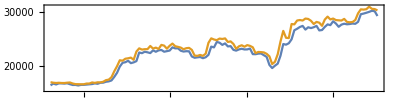
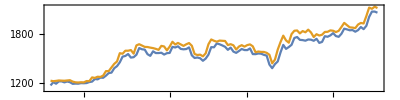
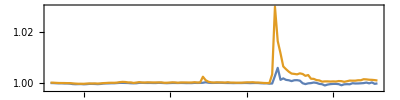
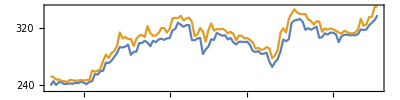
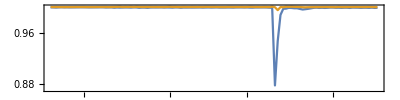
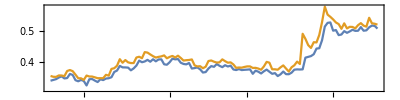
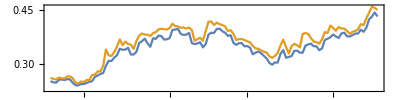
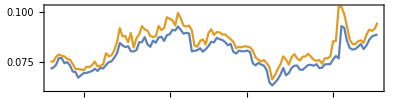
<|BTC-USD→-Graphics-,ETH-USD→-Graphics-,USDT-USD→-Graphics-,BNB-USD→-Graphics-,USDC-USD→-Graphics-,XRP-USD→-Graphics-,ADA-USD→-Graphics-,DOGE-USD→-Graphics-,STETH-USD→-Graphics-,HEX-USD→-Graphics-,MATIC-USD→-Graphics-,SOL-USD→-Graphics-,DOT-USD→-Graphics-,LTC-USD→-Graphics-,AVAX-USD→-Graphics-,SHIB-USD→-Graphics-,WTRX-USD→-Graphics-,BUSD-USD→-Graphics-,TRX-USD→-Graphics-,DAI-USD→-Graphics-,WBTC-USD→-Graphics-,LINK-USD→-Graphics-,UNI7083-USD→-Graphics-,ATOM-USD→-Graphics-,OKB-USD→-Graphics-|>

```mathematica
nDays=120;
Map[
Block[{dsTemp=#[Select[AbsoluteTime[#DateObject]>AbsoluteTime[DatePlus[Now,-Quantity[nDays,"Days"]]]&]]},
DateListPlot[{
Normal[dsTemp[All,{"DateObject","Low"}][Values]],
Normal[dsTemp[All,{"DateObject","High"}][Values]]},
PlotLegends->{"Low","High"},
AspectRatio->1/4,
PlotRange->All]
]&,
aCryptoCurrenciesData
]
```

Here we plot the volume time series for each crypto-currency for the last 120 days:

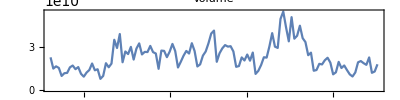
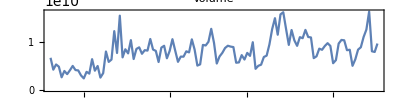
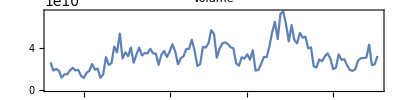
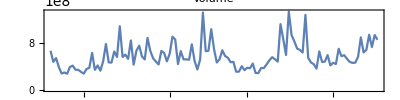
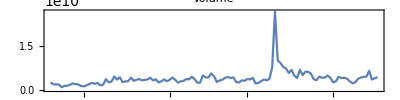
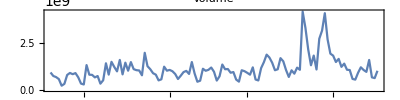
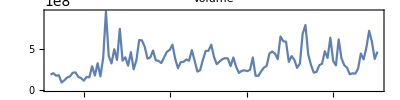
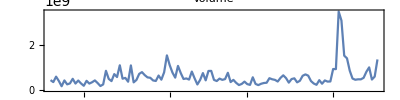
<|BTC-USD→-Graphics-,ETH-USD→-Graphics-,USDT-USD→-Graphics-,BNB-USD→-Graphics-,USDC-USD→-Graphics-,XRP-USD→-Graphics-,ADA-USD→-Graphics-,DOGE-USD→-Graphics-,STETH-USD→-Graphics-,HEX-USD→-Graphics-,MATIC-USD→-Graphics-,SOL-USD→-Graphics-,DOT-USD→-Graphics-,LTC-USD→-Graphics-,AVAX-USD→-Graphics-,SHIB-USD→-Graphics-,WTRX-USD→-Graphics-,BUSD-USD→-Graphics-,TRX-USD→-Graphics-,DAI-USD→-Graphics-,WBTC-USD→-Graphics-,LINK-USD→-Graphics-,UNI7083-USD→-Graphics-,ATOM-USD→-Graphics-,OKB-USD→-Graphics-|>

```mathematica
nDays=120;
Map[
Block[{dsTemp=#[Select[AbsoluteTime[#DateObject]>AbsoluteTime[DatePlus[Now,-Quantity[nDays,"Days"]]]&]]},
DateListPlot[{
Normal[dsTemp[All,{"DateObject","Volume"}][Values]]},
PlotLabel->"Volume",
AspectRatio->1/4,
PlotRange->All]
]&,
aCryptoCurrenciesData
]
```

## data.bitcoinity.org

In this section we ingest crypto-currency data from data.bitcoinity.org, [DBO1].

### Metadata

In this sub-section we assign different metadata elements used in data.bitcoinity.org.

The currencies and exchanges we obtained by examining the output of:

Import["https://data.bitcoinity.org/markets/price/30d/USD?t=l", "Plaintext"]

#### Assignments

```mathematica
lsCurrencies={"all","AED","ARS","AUD","BRL","CAD","CHF","CLP","CNY","COP","CZK","DKK","EUR","GBP","HKD","HRK","HUF","IDR","ILS","INR","IRR","JPY","KES","KRW","MXN","MYR","NOK","NZD","PHP","PKR","PLN","RON","RUB","RUR","SAR","SEK","SGD","THB","TRY","UAH","USD","VEF","XAU","ZAR"};
```

```mathematica
lsExchanges={"all","bit-x","bit2c","bitbay","bitcoin.co.id","bitcoincentral","bitcoinde","bitcoinsnorway","bitcurex","bitfinex","bitflyer","bithumb","bitmarketpl","bitmex","bitquick","bitso","bitstamp","btcchina","btce","btcmarkets","campbx","cex.io","clevercoin","coinbase","coinfloor","exmo","gemini","hitbtc","huobi","itbit","korbit","kraken","lakebtc","localbitcoins","mercadobitcoin","okcoin","paymium","quadrigacx","therocktrading","vaultoro","wallofcoins"};
```

```mathematica
lsTimeSpans={"10m","1h","6h","24h","3d","30d","6m","2y","5y","all"};
```

```mathematica
lsTimeUnit={"second","minute","hour","day","week","month"};
```

```mathematica
aDataTypeDescriptions=Association@{"price"->"Price","volume"->"Trading Volume","rank"->"Rank","bidask_sum"->"Bid/Ask Sum","spread"->"Bid/Ask Spread","tradespm"->"Trades Per Minute"};
lsDataTypes=Keys[aDataTypeDescriptions];
```

### Getting BTC data

Here we make a template string that for CSV data retrieval from data.bitcoinity.org:

```mathematica
stDBOURL=StringTemplate["https://data.bitcoinity.org/export_data.csv?currency=`currency`&data_type=`dataType`&exchange=`exchange`&r=`timeUnit`&t=l&timespan=`timeSpan`"]
```

TemplateObject[{https://data.bitcoinity.org/export_data.csv?currency=,TemplateSlot[currency],&data_type=,TemplateSlot[dataType],&exchange=,TemplateSlot[exchange],&r=,TemplateSlot[timeUnit],&t=l&timespan=,TemplateSlot[timeSpan]},CombinerFunction→StringJoin,InsertionFunction→TextString]

Here is an association with default values for the string template above:

```mathematica
aDBODefaultParameters=<|"currency"->"USD","dataType"->"price","exchange"->"all","timeUnit"->"day","timeSpan"->"all"|>;
```

Remark: The metadata assigned above is used to form valid queries for the query string template.

Remark: Not all combinations of parameters are “fully respected” by data.bitcoinity.org. For example, if a data request is with time granularity that is too fine over a large time span, then the returned data is with coarser granularity.

#### Price for a particular currency and exchange pair

Here we retrieve data by overwriting the parameters for currency, time unit, time span, and exchange:

```mathematica
dsBTCPriceData=
ResourceFunction["ImportCSVToDataset"][stDBOURL[Join[aDBODefaultParameters,<|"currency"->"EUR","timeUnit"->"hour","timeSpan"->"30d","exchange"->"coinbase"|>]]];
dsBTCPriceData=dsBTCPriceData[All,Join[<|"Symbol"->"BTC","DateObject"->DateObject[#Time]|>,#]&]
```

Here is a summary:

```mathematica
ResourceFunction["RecordsSummary"][dsBTCPriceData]
```

{1 Symbol
BTC | 719,2 DateObject
Min | Sun 19 Mar 2023 23:00:00GMT-4
1st Qu | Mon 27 Mar 2023 10:15:00GMT-4
Mean | Mon 3 Apr 2023 22:00:00GMT-4
Median | Mon 3 Apr 2023 22:00:00GMT-4
3rd Qu | Tue 11 Apr 2023 09:45:00GMT-4
Max | Tue 18 Apr 2023 21:00:00GMT-4,3 Time
2023-03-20 03:00:00 UTC | 1
2023-03-20 04:00:00 UTC | 1
2023-03-20 05:00:00 UTC | 1
2023-03-20 06:00:00 UTC | 1
2023-03-20 07:00:00 UTC | 1
2023-03-20 08:00:00 UTC | 1
(Other) | 713,4 avg
Min | 24758.4
1st Qu | 25698.2
Median | 26054.1
Mean | 26285.5
3rd Qu | 27019.3
Max | 27916.1,5 max
Min | 24840.2
1st Qu | 25761.7
Median | 26152.1
Mean | 26369.1
3rd Qu | 27084.8
Max | 28050.1,6 min
Min | 24550.
1st Qu | 25622.4
Median | 25955.8
Mean | 26197.7
3rd Qu | 26971.
Max | 27849.7}

#### Volume data

Here we retrieve data by overwriting the parameters for data type, time unit, time span, and exchange:

```mathematica
Print@stDBOURL[Join[aDBODefaultParameters,<|"dataType"->Volume,"timeUnit"->"day","timeSpan"->"30d","exchange"->"coinbase"|>]]
```

https://data.bitcoinity.org/export_data.csv?currency=USD&data_type=Volume&exchange=coinbase&r=day&t=l&timespan=30d

```mathematica
ResourceFunction["ImportCSVToDataset"][stDBOURL[Join[aDBODefaultParameters,<|"dataType"->Volume,"timeUnit"->"day","timeSpan"->"30d","exchange"->"coinbase"|>]]]
```

```mathematica
dsBTCVolumeData=
ResourceFunction["ImportCSVToDataset"][stDBOURL[Join[aDBODefaultParameters,<|"dataType"->Volume,"timeUnit"->"day","timeSpan"->"30d","exchange"->"coinbase"|>]]];
dsBTCVolumeData=dsBTCVolumeData[All,Join[<|"Symbol"->"BTC","DateObject"->DateObject[#Time]|>,#]&]
```

Here is a summary:

```mathematica
ResourceFunction["RecordsSummary"][dsBTCVolumeData]
```

{1 Symbol
BTC | 30,2 DateObject
Min | Sun 19 Mar 2023 20:00:00GMT-4
1st Qu | Sun 26 Mar 2023 20:00:00GMT-4
Mean | Mon 3 Apr 2023 08:00:00GMT-4
Median | Mon 3 Apr 2023 08:00:00GMT-4
3rd Qu | Mon 10 Apr 2023 20:00:00GMT-4
Max | Mon 17 Apr 2023 20:00:00GMT-4,3 Time
2023-03-20 00:00:00 UTC | 1
2023-03-21 00:00:00 UTC | 1
2023-03-22 00:00:00 UTC | 1
2023-03-23 00:00:00 UTC | 1
2023-03-24 00:00:00 UTC | 1
2023-03-25 00:00:00 UTC | 1
(Other) | 24,4 
Min | 3854.33
1st Qu | 9655.95
Mean | 14466.2
Median | 14532.5
3rd Qu | 18637.2
Max | 33862.9}

```mathematica
RecordsSummary[ResourceFunction["ImportCSVToDataset"][stDBOURL[Join[aDBODefaultParameters,<|"dataType"->Volume,"timeUnit"->"day","timeSpan"->"all","exchange"->"all"|>]]]]
```

{1 Time
2010-07-17 00:00:00 UTC | 1
2010-07-18 00:00:00 UTC | 1
2010-07-19 00:00:00 UTC | 1
2010-07-20 00:00:00 UTC | 1
2010-07-21 00:00:00 UTC | 1
2010-07-22 00:00:00 UTC | 1
(Other) | 4653,2 bit-x
 | 2362
0.0001 | 6
0.0003 | 4
0.0006 | 3
0.001 | 3
0.0013 | 3
(Other) | 2278,3 bitfinex
 | 974
242.502 | 1
282.768 | 1
323.101 | 1
334.334 | 1
356.98 | 1
(Other) | 3680,4 bitstamp
 | 455
11. | 2
0.25 | 1
0.295858 | 1
0.3 | 1
0.5 | 1
(Other) | 4198,5 btce
 | 2887
1. | 1
10.7837 | 1
160.824 | 1
202.697 | 1
310.811 | 1
(Other) | 1767,6 coinbase
 | 1645
0.01 | 1
0.015 | 1
0.02 | 1
0.04 | 1
0.0565555 | 1
(Other) | 3009,7 gemini
 | 1910
14.4878 | 1
17.1756 | 1
31.7547 | 1
39.3488 | 1
48.8417 | 1
(Other) | 2744,8 kraken
 | 1189
0.1 | 3
2. | 2
0.00003811 | 1
0.00063515 | 1
0.00159536 | 1
(Other) | 3462,9 mtgox
 | 3495
0.25 | 1
0.4 | 1
2. | 1
2.1 | 1
2.6 | 1
(Other) | 1159,10 okcoin
 | 3484
7.68 | 1
36.941 | 1
81.493 | 1
88.934 | 1
91.138 | 1
(Other) | 1170,11 others
 | 350
1. | 2
1.1 | 1
2.35 | 1
3.3 | 1
4. | 1
(Other) | 4303}

### Plots

#### Price data

Here we extract the non-time columns in the tabular price data obtained above and plot the corresponding time series:

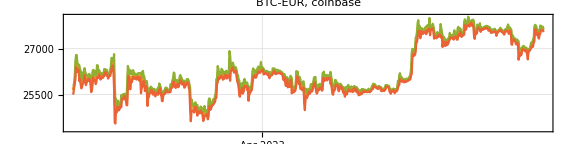

```mathematica
DateListPlot[Association[#->Normal[dsBTCPriceData[All,{"DateObject",#}][Values]]&/@Take[Normal[Keys[dsBTCPriceData⟦1⟧]],{3,-1}]],AspectRatio->1/4,ImageSize->Large,PlotLabel->Row[{"BTC-EUR, coinbase"}],PlotTheme->"Detailed"]
```

#### Volume data

Here we extract the non-time columns (corresponding to exchanges) in the tabular volume data obtained above and plot the corresponding time series:

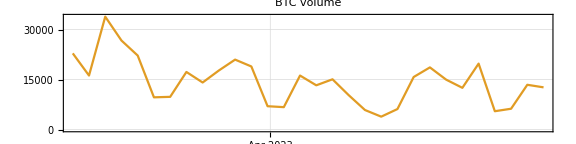

```mathematica
DateListPlot[Association[#->Normal[dsBTCVolumeData[All,{"DateObject",#}][Values]]&/@Take[Normal[Keys[dsBTCVolumeData⟦1⟧]],{3,-1}]],PlotRange->All,AspectRatio->1/4,ImageSize->Large,PlotLabel->Row[{"BTC volume"}],PlotTheme->"Detailed",GridLines->Automatic]
```

## References

[DBO1] https://data.bitcoinity.org.

[WK1] Wikipedia entry, Cryptocurrency.

[YF1] Yahoo! Finance, Cryptocurrencies.

Related Guides

Related Tech Notes

Cryptocurrencies data explorations

## Metadata

### Categorization

Tech Note

AntonAntonov/CryptocurrencyData

AntonAntonov`CryptocurrencyData`

AntonAntonov/CryptocurrencyData/tutorial/Crypto-currenciesdataacquisitionwithvisualization

### Keywords

Cryptocurrency, Ingestion